```mathematica
h = 6.6261963*10^-35 (*Jerk-sh*)
```

6.6262×10^-35

```mathematica
k=1.6021917*10^-25 (*Jrk/keV*)
```

1.60219×10^-25

```mathematica
c = 299.792458 (*cm/sh*)
```

299.792

```mathematica
B[ν_,T_]:= (2 k^4 ν^3)/(h^3c^2) 1/(Exp[ν/(T)]-1) (*Clark,JCP 70,no.2 1987,p 316*)
```

```mathematica
opacf[ν_]:= Piecewise[{{24,ν<3},{54,ν≥ 3}}]
```

```mathematica
σ[ν_,T_]:=opacf[ν]*1/ν^3(1-Exp[-ν/T])
```

```mathematica
tb[Z_,μ_,v_,t_,L_]:=Max[ (μ c t - Z)/(μ c - v),0]
```

```mathematica
tf[Z_,μ_,v_,t_,L_]:=Max[ (L+(μ c t - Z))/(μ c - v),0]
```

```mathematica
s[Z_,μ_,v_,t_,L_]:=Max[c*(tf[Z,μ,v,t,L]-tb[Z,μ,v,t,L]) ,0]
```

```mathematica
logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
groupBounds=logspace[Log[10^-3],Log[30],51];
groupWidths = Differences[groupBounds];
groupGmid=Table[GeometricMean[groupBounds[[i;;i+1]]],{i,1,50}];
```

```mathematica
Tval = 1 (*keV*)
```

1

```mathematica
N[groupBounds]
```

{0.001,0.00122897,0.00151038,0.00185621,0.00228123,0.00280357,0.00344552,0.00423445,0.00520403,0.00639561,0.00786003,0.00965977,0.0118716,0.0145899,0.0179306,0.0220362,0.0270819,0.0332829,0.0409038,0.0502697,0.0617801,0.0759261,0.0933111,0.114677,0.140935,0.173205,0.212864,0.261605,0.321505,0.395121,0.485593,0.596781,0.733428,0.901364,1.10775,1.3614,1.67312,2.05622,2.52704,3.10566,3.81678,4.69072,5.76477,7.08475,8.70696,10.7006,13.1508,16.162,19.8626,24.4106,30.}

```mathematica
opacsGmid=Table[Evaluate[σ[groupGmid[[j]],Tval]],{j,1,50}];
```

Part::pkspec1: The expression j cannot be used as a part specification.

```mathematica
pcf = Table[{opacsGmid[[i]],ν<groupBounds[[i]]&& ν≤ groupBounds[[i+1]]},{i,1,50}];
opacPiece = Piecewise[pcf];
```

```mathematica
opacfunc[νt_]:=opacPiece/.ν->νt
```

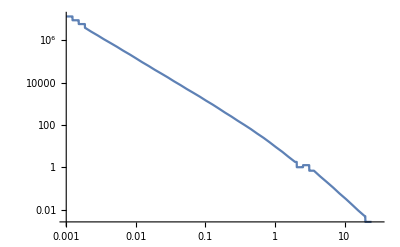

```mathematica
LogLogPlot[opacfunc[x],{x,0.001,30}]
```

```mathematica
Iz[Z_,μ_,ν_,v_,t_,L_,T_]:= B[γ Dl ν, T]/(γ Dl)^3(1-Exp[-γ Dl (opacfunc[ν*γ*Dl]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
IzNoMult[Z_,μ_,ν_,v_,t_,L_,T_]:= B[ν, T]/(γ Dl)^3(1-Exp[-γ Dl (opacfunc[ν]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
spect=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,5.994,1,4,Tval]],{μ,(-4+12)/(c 1),1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->10, MaxRecursion->50,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,35,45}]
```

{{1.22804,0.000807325},{1.50923,0.00102705},{1.85481,0.00124633},{2.27951,0.001419},{2.80145,0.00149845},{3.44291,0.00140874},{4.23125,0.00110939},{5.20009,0.000681342},{6.39077,0.000309657},{7.85408,0.000100085},{9.65246,0.0000220251}}

```mathematica
specNov=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,5.994*0,1,4,Tval]],{μ,(-4+12)/(c 1),1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->10, MaxRecursion->50,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,35,45}]
```

{{1.22804,0.00079318},{1.50923,0.00100699},{1.85481,0.00121872},{2.27951,0.00138243},{2.80145,0.00145386},{3.44291,0.00135717},{4.23125,0.00105612},{5.20009,0.000637453},{6.39077,0.000283358},{7.85408,0.0000890683},{9.65246,0.0000188665}}

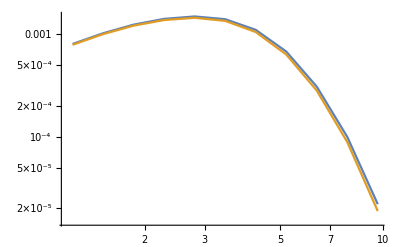

```mathematica
ListLogLogPlot[{spect,specNov},Joined->True]
```

```mathematica
(*Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,5.994,1,4,Tval]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->12, MaxRecursion->50,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,50}]*)
```